```mathematica
SetDirectory[NotebookDirectory[]];
<<bipartiteSUSY.m
```

```mathematica
(*These are ALL the Kasteleyns:           -------->     -------->     -------->     -------->     -------->     -------->  *)
```

```mathematica
(*-------------------------------------------------------------------------------------------------*)
(*There are currently 104 different examples (highest is Subscript[bft, 104]). If you introduce any more, call the next one 105, and update this number! *)
(*Rules: 'a' is the upper left matrix, 'b' is the upper right, 'c' is the lower left, 'd' is the lower right. You have to label the internal faces first, Then external ones. You have to label First the internal white nodes, then external white nodes, then internal black nodes, then external black nodes.  *)
(*-------------------------------------------------------------------------------------------------*)

(*-------------------------------------------------------------------------------------------------*)
(*---------------------GENUS ZERO, ONE BOUNDARY CASES, I.E. THE DISK-----------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Normal square box.*)
Subscript[bft, 1]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1]},{Subscript[X, 5,1],Subscript[X, 1,4]}};
b={{Subscript[X, 2,3],0},{0,Subscript[X, 4,5]}};
c={{Subscript[X, 2,5],0},{0,Subscript[X, 4,3]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Square box with crossed legs*)
Subscript[bft, 2]:=(
a={{Subscript[X, 3,1],Subscript[X, 1,2]},{Subscript[X, 1,4],Subscript[X, 4,1]}};
b={{Subscript[X, 2,3],0},{0,Subscript[X, 1,1]}};
c={{0,Subscript[X, 2,4]},{Subscript[X, 4,3],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Double square box, i.e. the unreduced Gr(2,4).*)
Subscript[bft, 3]:=(
a={{Subscript[X, 3,1],Subscript[X, 1,2],Subscript[X, 2,3]},{Subscript[X, 1,4],Subscript[X, 5,1],0},{0,Subscript[X, 2,5],Subscript[X, 6,2]}};
b={{0,0},{0,Subscript[X, 4,5]},{Subscript[X, 5,6],0}};
c={{0,0,Subscript[X, 3,6]},{Subscript[X, 4,3],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Double square box with Subscript[X, 6,2] Higgsed.*)
Subscript[bft, 4]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1],Subscript[X, 2,3]},{Subscript[X, 5,1],Subscript[X, 1,4],0},{Subscript[X, 2,5],0,0}};
b={{0,0},{0,Subscript[X, 4,5]},{Subscript[X, 5,2],0}};
c={{0,0,Subscript[X, 3,2]},{0,Subscript[X, 4,3],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Double square box, with face 2 being a confinement bubble.*)
Subscript[bft, 5]:=(
a={{Subscript[X, 6,2]+Subscript[X, 2,1],Subscript[X, 1,5]},{Subscript[X, 1,3],Subscript[X, 4,1]}};
b={{Subscript[X, 5,6],0},{0,Subscript[X, 3,4]}};
c={{Subscript[X, 3,6],0},{0,Subscript[X, 5,4]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Normal planar Gr(3,5).*)
Subscript[bft, 6]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1],Subscript[X, 2,3]},{Subscript[X, 5,1],Subscript[X, 1,4],0},{Subscript[X, 2,6],0,Subscript[X, 7,2]}};
b={{0,0},{0,Subscript[X, 4,5]},{Subscript[X, 6,7],0}};
c={{0,0,Subscript[X, 3,7]},{0,Subscript[X, 4,3],0},{Subscript[X, 6,5],0,0}};
d={{0,0},{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Normal planar Gr(2,5).*)
Subscript[bft, 73]:=(
a={{Subscript[X, 7,2],Subscript[X, 2,3],0},{Subscript[X, 2,6],Subscript[X, 1,2],Subscript[X, 5,1]},{0,Subscript[X, 3,1],Subscript[X, 1,4]}};
b={{Subscript[X, 3,7],0,0},{0,0,Subscript[X, 6,5]},{0,Subscript[X, 4,3],0}};
c={{Subscript[X, 6,7],0,0},{0,0,Subscript[X, 4,5]}};
d={{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*2 gluon, 2 loop on a disk. CONTAINS SELF-INTERSECTING ZIGZAGS!*)
Subscript[bft, 7]:=(
a={{Subscript[X, 3,1]+Subscript[X, 1,2]+Subscript[X, 2,4]}};
b={{Subscript[X, 4,3]}};
c={{Subscript[Y, 4,3]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*3 gluon, 3 loop on a disk. CONTAINS SELF-INTERSECTING ZIGZAGS!*)
Subscript[bft, 8]:=(
a={{Subscript[X, 3,1],Subscript[X, 1,5]},{Subscript[X, 2,4],Subscript[X, 5,2]},{Subscript[X, 1,2],Subscript[X, 2,1]}};
b={{Subscript[X, 5,3],0},{0,Subscript[X, 4,5]},{0,0}};
c={{Subscript[X, 4,3],0}};
d={{0,0}};
drawBFT[a,b,c,d]
)

(*Top cell of Gr(2,6).*)
Subscript[bft, 9]:=(
a={{Subscript[X, 9,1],Subscript[X, 1,8],0,0},{0,Subscript[X, 8,2],Subscript[X, 2,7],0},{0,0,Subscript[X, 7,3],Subscript[X, 3,6]},{Subscript[X, 1,4],Subscript[X, 2,1],Subscript[X, 3,2],Subscript[X, 5,3]}};
b={{Subscript[X, 8,9],0,0,0},{0,Subscript[X, 7,8],0,0},{0,0,Subscript[X, 6,7],0},{0,0,0,Subscript[X, 4,5]}};
c={{Subscript[X, 4,9],0,0,0},{0,0,0,Subscript[X, 6,5]}};
d={{0,0,0,0},{0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Top cell of Gr(3,6).*)
Subscript[bft, 10]:=(
a={{Subscript[X, 5,2],Subscript[X, 2,10],0,0,0,0},{Subscript[X, 2,6],Subscript[X, 1,2],Subscript[X, 6,1],0,0,0},{0,0,Subscript[X, 3,6],0,0,Subscript[X, 7,3]},{0,0,Subscript[X, 1,3],Subscript[X, 8,1],0,Subscript[X, 3,8]},{0,Subscript[X, 10,1],0,Subscript[X, 1,4],Subscript[X, 4,10],0},{0,0,0,Subscript[X, 4,8],Subscript[X, 9,4],0}};
b={{Subscript[X, 10,5],0,0},{0,0,0},{0,Subscript[X, 6,7],0},{0,0,0},{0,0,0},{0,0,Subscript[X, 8,9]}};
c={{Subscript[X, 6,5],0,0,0,0,0},{0,0,0,0,0,Subscript[X, 8,7]},{0,0,0,0,Subscript[X, 10,9],0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*7-dimensional Gr(3,6).*)
Subscript[bft, 11]:=(
a={{Subscript[X, 3,1],0,0,Subscript[X, 1,8]},{Subscript[X, 1,4],Subscript[X, 4,2],Subscript[X, 2,1],0},{0,Subscript[X, 2,5],Subscript[X, 6,2],0},{0,0,Subscript[X, 1,6],Subscript[X, 7,1]}};
b={{Subscript[X, 8,3],0,0},{0,0,0},{0,Subscript[X, 5,6],0},{0,0,Subscript[X, 6,7]}};
c={{Subscript[X, 4,3],0,0,0},{0,Subscript[X, 5,4],0,0},{0,0,0,Subscript[X, 8,7]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Top cell of Gr(2,7).*)
Subscript[bft, 12]:=(
a={{Subscript[X, 11,1],Subscript[X, 1,10],0,0,0},{0,Subscript[X, 10,2],Subscript[X, 2,9],0,0},{0,0,Subscript[X, 9,3],Subscript[X, 3,8],0},{0,0,0,Subscript[X, 8,4],Subscript[X, 4,7]},{Subscript[X, 1,5],Subscript[X, 2,1],Subscript[X, 3,2],Subscript[X, 4,3],Subscript[X, 6,4]}};
b={{Subscript[X, 10,11],0,0,0,0},{0,Subscript[X, 9,10],0,0,0},{0,0,Subscript[X, 8,9],0,0},{0,0,0,Subscript[X, 7,8],0},{0,0,0,0,Subscript[X, 5,6]}};
c={{Subscript[X, 5,11],0,0,0,0},{0,0,0,0,Subscript[X, 7,6]}};
d={{0,0,0,0,0},{0,0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Top cell of Gr(3,7).*)
Subscript[bft, 13]:=(
a={{Subscript[X, 1,7],Subscript[X, 2,1],Subscript[X, 3,2],Subscript[X, 8,3],0,0,0},{Subscript[X, 13,1],Subscript[X, 1,4],0,0,Subscript[X, 4,13],0,0},{0,Subscript[X, 4,2],Subscript[X, 2,5],0,0,Subscript[X, 5,4],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,6],0,0,Subscript[X, 6,5]},{0,0,0,0,Subscript[X, 12,4],Subscript[X, 4,11],0},{0,0,0,0,0,Subscript[X, 11,5],Subscript[X, 5,10]},{0,0,0,Subscript[X, 6,9],0,0,Subscript[X, 10,6]}};
b={{0,0,0,Subscript[X, 7,8]},{0,0,0,0},{0,0,0,0},{0,0,0,0},{Subscript[X, 11,12],0,0,0},{0,Subscript[X, 10,11],0,0},{0,0,Subscript[X, 9,10],0}};
c={{Subscript[X, 7,13],0,0,0,0,0,0},{0,0,0,Subscript[X, 9,8],0,0,0},{0,0,0,0,Subscript[X, 13,12],0,0}};
d={{0,0,0,0},{0,0,0,0},{0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Permutation {4,5,6,7,8,9} (bipartite) under scheme 0.*)
Subscript[bft, 14]:=(
a={{Subscript[X, 6,2],0,Subscript[X, 2,3],Subscript[X, 3,5],0},{Subscript[X, 2,7],Subscript[X, 7,1],Subscript[X, 1,2],0,0},{0,Subscript[X, 1,8],0,0,Subscript[X, 9,1]},{0,0,Subscript[X, 3,1],Subscript[X, 4,3],Subscript[X, 1,4]},{0,0,0,Subscript[X, 10,4],Subscript[X, 4,9]}};
b={{Subscript[X, 5,6],0,0},{0,0,0},{0,Subscript[X, 8,9],0},{0,0,0},{0,0,Subscript[X, 9,10]}};
c={{Subscript[X, 7,6],0,0,0,0},{0,Subscript[X, 8,7],0,0,0},{0,0,0,Subscript[X, 5,10],0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Permutation {4,5,6,7,8,9} (bipartite) under scheme 1.*)
Subscript[bft, 15]:=(
a={{Subscript[X, 6,2],0,Subscript[X, 2,3],Subscript[X, 3,5],0},{Subscript[X, 2,7],Subscript[X, 7,1],Subscript[X, 1,2],0,0},{0,Subscript[X, 1,8],Subscript[X, 4,1],0,Subscript[X, 9,4]},{0,0,Subscript[X, 3,4],Subscript[X, 10,3],Subscript[X, 4,10]}};
b={{Subscript[X, 5,6],0},{0,0},{0,Subscript[X, 8,9]},{0,0}};
c={{0,0,0,0,Subscript[X, 10,9]},{Subscript[X, 7,6],0,0,0,0},{0,Subscript[X, 8,7],0,0,0},{0,0,0,Subscript[X, 5,10],0}};
d={{0,0},{0,0},{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*---------------------GENUS ZERO, MULTI BOUNDARY CASES, I.E. NON-PLANAR-------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*G(3,6) top-dim guy with B=2 and two strange poles*)
Subscript[bft, 75]:=(
a={{Subscript[X, 8,1],Subscript[X, 1,7],0,0,0,0},{0,Subscript[X, 2,1],0,0,Subscript[X, 4,2],Subscript[X, 1,4]},{Subscript[X, 1,9],0,Subscript[X, 9,3],Subscript[X, 3,6],0,Subscript[X, 6,1]},{0,Subscript[X, 7,2],Subscript[X, 3,7],Subscript[X, 2,3],0,0},{0,0,0,Subscript[X, 6,2],Subscript[X, 2,5],0}};
b={{Subscript[X, 7,8],0},{0,0},{0,0},{0,0},{0,Subscript[X, 5,6]}};
c={{Subscript[X, 9,8],0,0,0,0,0},{0,0,Subscript[X, 7,9],0,0,0},{0,0,0,0,0,Subscript[X, 4,6]},{0,0,0,0,Subscript[X, 5,4],0}};
d={{0,0},{0,0},{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*G(3,6) top-dim guy with B=2 and one strange poles*)
Subscript[bft, 76]:=(
a={{Subscript[X, 9,1],Subscript[X, 1,5],0,0,Subscript[X, 5,9],0},{Subscript[X, 1,6],Subscript[X, 2,1],Subscript[X, 6,2],0,0,0},{0,Subscript[X, 5,2],0,Subscript[X, 2,4],0,0},{0,0,0,Subscript[X, 4,3],Subscript[X, 3,5],0},{0,0,Subscript[X, 2,7],Subscript[X, 3,2],0,Subscript[X, 7,3]},{0,0,0,0,Subscript[X, 9,3],Subscript[X, 3,8]}};
b={{0,0,0},{0,0,0},{0,Subscript[X, 4,5],0},{Subscript[X, 5,4],0,0},{0,0,0},{0,0,Subscript[X, 8,9]}};
c={{Subscript[X, 6,9],0,0,0,0,0},{0,0,Subscript[X, 7,6],0,0,0},{0,0,0,0,0,Subscript[X, 8,7]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Standard example on a cylinder which reduces to sums of square boxes.*)
Subscript[bft, 16]:=(
a={{Subscript[X, 1,3],Subscript[X, 3,1],0},{0,Subscript[X, 1,2],Subscript[X, 2,1]},{0,Subscript[X, 2,3],Subscript[X, 4,2]},{Subscript[X, 5,1],0,Subscript[X, 1,4]}};
b={{0,0,0},{Subscript[X, 2,2],0,0},{0,Subscript[X, 3,4],0},{0,0,Subscript[X, 4,5]}};
c={{Subscript[X, 3,5],0,0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Standard example on a cylinder, after a flip manoever.*)
Subscript[bft, 17]:=(
a={{Subscript[X, 1,3],Subscript[X, 3,1],0},{0,Subscript[X, 1,2],Subscript[X, 2,1]},{0,Subscript[X, 2,3],Subscript[X, 4,2]},{Subscript[X, 5,1],0,Subscript[X, 1,4]}};
b={{0,0,0},{Subscript[X, 2,2],0,0},{0,Subscript[X, 3,4],0},{0,0,Subscript[X, 4,5]}};
c={{Subscript[X, 3,5],0,0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Standard example on a cylinder, with massive node integrated out.*)
Subscript[bft, 18]:=(
a={{Subscript[X, 3,2],Subscript[X, 2,5]},{Subscript[X, 2,1],Subscript[X, 1,2]},{Subscript[X, 1,4],Subscript[X, 5,1]}};
b={{Subscript[X, 5,3],0,0},{0,0,Subscript[X, 2,2]},{0,Subscript[X, 4,5],0}};
c={{Subscript[X, 4,3],0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Standard example on a cylinder, with massive node integrated out and a flip manoever..*)
Subscript[bft, 19]:=(
a={{Subscript[X, 3,2],Subscript[X, 2,5]},{Subscript[X, 2,1],Subscript[X, 1,2]},{Subscript[X, 1,4],Subscript[X, 5,1]}};
b={{Subscript[X, 5,3],0,0},{0,0,Subscript[X, 1,1]},{0,Subscript[X, 4,5],0}};
c={{Subscript[X, 4,3],0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Similar to standard example, this is a 6 gluon, 1 loop on a cylinder. It is reduced.*)
Subscript[bft, 20]:=(
a={{Subscript[X, 2,4],Subscript[X, 4,2],0,0},{0,Subscript[X, 2,1],0,Subscript[X, 1,3]},{0,Subscript[X, 1,4],0,Subscript[X, 5,1]},{Subscript[X, 6,2],0,Subscript[X, 3,6],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,5]}};
b={{0,0,0},{0,Subscript[X, 3,2],0},{0,0,Subscript[X, 4,5]},{Subscript[X, 2,3],0,0},{0,0,0}};
c={{Subscript[X, 4,6],0,0,0},{0,0,Subscript[X, 6,5],0}};
d={{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Simpler than standard example: 3 gluon, 1 loop on a cylinder.*)
Subscript[bft, 21]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,2],0},{0,Subscript[X, 2,1],Subscript[X, 1,2]},{0,Subscript[X, 1,3],Subscript[X, 4,1]},{Subscript[X, 5,2],0,Subscript[X, 2,4]}};
b={{0,0,0},{0,0,Subscript[X, 2,2]},{0,Subscript[X, 3,4],0},{Subscript[X, 4,5],0,0}};
c={{Subscript[X, 3,5],0,0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Simplest nonplanar cylinder guy (intrinsically nonplanar).*)
Subscript[bft, 22]:=(
a={{Subscript[X, 6,2],Subscript[X, 2,1],Subscript[X, 1,6],0},{Subscript[X, 3,6],Subscript[X, 1,3],0,Subscript[X, 6,1]},{0,0,Subscript[X, 4,1],Subscript[X, 1,5]}};
b={{0},{0},{Subscript[X, 5,4]}};
c={{Subscript[X, 2,3],0,0,0},{0,Subscript[X, 3,2],0,0},{0,0,Subscript[X, 6,4],0},{0,0,0,Subscript[X, 5,6]}};
d={{0},{0},{0},{0}};
drawBFT[a,b,c,d]
)

(*Slightly more complicated intrinsically nonplanar guy on the cylinder.*)
Subscript[bft, 23]:=(
a={{Subscript[X, 2,4],Subscript[X, 4,2],0,0},{0,Subscript[X, 2,1],0,Subscript[X, 1,3]},{0,Subscript[X, 1,4],0,Subscript[X, 5,1]},{Subscript[X, 6,2],0,Subscript[X, 3,6],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,5]}};
b={{0,0,0},{0,Subscript[X, 3,2],0},{0,0,Subscript[X, 4,5]},{Subscript[X, 2,3],0,0},{0,0,0}};
c={{Subscript[X, 4,6],0,0,0},{0,0,Subscript[X, 6,5],0}};
d={{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Y2,0 with a periodic direction cut out (i.e. on cylinder).*)
Subscript[bft, 24]:=(
a={{Subscript[X, 5,2]+Subscript[X, 1,4],Subscript[X, 2,1]},{Subscript[Y, 2,1],Subscript[X, 3,2]+Subscript[X, 1,6]}};
b={{0,Subscript[X, 4,5]},{Subscript[X, 6,3],0}};
c={{0,Subscript[Y, 6,3]},{Subscript[Y, 4,5],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y4,0 with a periodic direction cut out (i.e. on cylinder).*)
Subscript[bft, 25]:=(
a={{Subscript[X, 7,1]+Subscript[X, 4,8],Subscript[X, 1,4],0,0},{Subscript[Y, 1,4],Subscript[X, 2,1]+Subscript[X, 4,5],Subscript[Y, 5,2],0},{0,Subscript[X, 5,2],Subscript[X, 2,3]+Subscript[X, 6,5],Subscript[X, 3,6]},{0,0,Subscript[Y, 3,6],Subscript[X, 9,3]+Subscript[X, 6,10]}};
b={{Subscript[X, 8,7],0},{0,0},{0,0},{0,Subscript[X, 10,9]}};
c={{Subscript[Y, 8,7],0,0,0},{0,0,0,Subscript[Y, 10,9]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*This is Y6,0 with one periodic direction cut out (ie on cylinder).*)
Subscript[bft, 26]:=(
a={{Subscript[X, 11,1]+Subscript[X, 6,12],Subscript[X, 1,6],0,0,0,0},{Subscript[Y, 1,6],Subscript[X, 2,1]+Subscript[X, 6,7],Subscript[Y, 7,2],0,0,0},{0,Subscript[X, 7,2],Subscript[X, 2,3]+Subscript[X, 8,7],Subscript[X, 3,8],0,0},{0,0,Subscript[Y, 3,8],Subscript[X, 4,3]+Subscript[X, 8,9],Subscript[Y, 9,4],0},{0,0,0,Subscript[X, 9,4],Subscript[X, 4,5]+Subscript[X, 10,9],Subscript[X, 5,10]},{0,0,0,0,Subscript[Y, 5,10],Subscript[X, 13,5]+Subscript[X, 10,14]}};
b={{Subscript[X, 12,11],0},{0,0},{0,0},{0,0},{0,0},{0,Subscript[X, 14,13]}};
c={{Subscript[Y, 12,11],0,0,0,0,0},{0,0,0,0,0,Subscript[Y, 14,13]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Reduction of square torus chopping THREE lines, is a 6 gluon 3 loops on a cylinder.*)
Subscript[bft, 27]:=(
a={{Subscript[X, 1,3],Subscript[X, 4,1],Subscript[X, 3,4],0},{0,Subscript[X, 1,5],Subscript[X, 6,2],Subscript[X, 2,1]},{Subscript[X, 3,7],0,Subscript[X, 2,3],Subscript[X, 9,2]},{Subscript[X, 7,1],0,0,Subscript[X, 1,8]}};
b={{0,0,0},{Subscript[X, 5,6],0,0},{0,0,Subscript[X, 7,9]},{0,Subscript[X, 8,7],0}};
c={{0,Subscript[X, 5,4],0,0},{0,0,Subscript[X, 4,6],0},{0,0,0,Subscript[X, 8,9]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Reduction of square torus chopping THREE lines, and Seiberg-dualizing face 2, is a 6 gluon 3 loops on a cylinder.*)
Subscript[bft, 28]:=(
a={{Subscript[X, 1,3],Subscript[X, 4,1],Subscript[X, 3,4],0,0,0},{0,Subscript[X, 1,5],0,0,Subscript[X, 6,1],0},{Subscript[X, 3,7],0,0,0,0,Subscript[X, 9,3]},{Subscript[X, 7,1],0,0,Subscript[X, 1,8],0,0},{0,0,Subscript[X, 6,3],0,Subscript[X, 2,6],Subscript[X, 3,2]},{0,0,0,Subscript[X, 9,1],Subscript[X, 1,2],Subscript[X, 2,9]}};
b={{0,0,0},{Subscript[X, 5,6],0,0},{0,0,Subscript[X, 7,9]},{0,Subscript[X, 8,7],0},{0,0,0},{0,0,0}};
c={{0,Subscript[X, 5,4],0,0,0,0},{0,0,Subscript[X, 4,6],0,0,0},{0,0,0,Subscript[X, 8,9],0,0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Rather complicated 6 gluon, 3 loop on a cylinder.*)
Subscript[bft, 29]:=(
a={{Subscript[X, 4,1],0,Subscript[X, 1,6],0,0,0},{Subscript[X, 2,4],Subscript[X, 5,2],0,0,0,0},{0,Subscript[X, 3,5],Subscript[X, 6,3],0,0,0},{Subscript[X, 1,2],0,0,Subscript[X, 7,1],Subscript[X, 2,7],0},{0,Subscript[X, 2,3],0,0,Subscript[X, 8,2],Subscript[X, 3,8]},{0,0,Subscript[X, 3,1],Subscript[X, 1,9],0,Subscript[X, 9,3]}};
b={{Subscript[X, 6,4],0,0},{0,Subscript[X, 4,5],0},{0,0,Subscript[X, 5,6]},{0,0,0},{0,0,0},{0,0,0}};
c={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,Subscript[X, 7,8],0},{0,0,0,0,0,Subscript[X, 8,9]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Another 6 gluon, 3 loop on a cylinder.*)
Subscript[bft, 30]:=(
a={{Subscript[X, 4,3],0,Subscript[X, 3,6],0,0,0},{Subscript[X, 2,4],Subscript[X, 5,2],0,0,0,0},{0,Subscript[X, 1,5],Subscript[X, 6,1],0,0,0},{0,0,0,Subscript[X, 7,3],Subscript[X, 2,7],0},{0,Subscript[X, 2,1],0,0,Subscript[X, 8,2],Subscript[X, 1,8]},{0,0,Subscript[X, 1,3],Subscript[X, 3,9],0,Subscript[X, 9,1]}};
b={{Subscript[X, 6,4],0,0,0},{0,Subscript[X, 4,5],0,0},{0,0,Subscript[X, 5,6],0},{0,0,0,Subscript[X, 3,2]},{0,0,0,0},{0,0,0,0}};
c={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,Subscript[X, 7,8],0},{0,0,0,0,0,Subscript[X, 8,9]},{Subscript[Y, 3,2],0,0,0,0,0}};
d={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Reduction of the square torus with a single boundary chopping THREE lines. It lives on a cylinder.*)
Subscript[bft, 31]:=(
a={{Subscript[X, 6,2],Subscript[X, 3,4],Subscript[X, 2,3],0},{Subscript[X, 1,5],Subscript[X, 4,1],0,0},{Subscript[X, 2,1],0,Subscript[X, 9,2],Subscript[X, 1,8]},{0,Subscript[X, 1,3],Subscript[X, 3,7],Subscript[X, 7,1]}};
b={{Subscript[X, 4,6],0,0},{0,Subscript[X, 5,4],0},{0,0,Subscript[X, 8,9]},{0,0,0}};
c={{Subscript[X, 5,6],0,0,0},{0,0,Subscript[X, 7,9],0},{0,0,0,Subscript[X, 8,7]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Has 3 boundaries, but is reducible. It's a top cell of Gr(3,5). It's a 'reduction' of the monster guy below.*)
Subscript[bft, 69]:=(
a={{Subscript[X, 7,1],Subscript[X, 1,6],0,0,0},{Subscript[X, 1,3],Subscript[X, 3,1],0,0,0},{Subscript[X, 3,7],0,Subscript[X, 4,3],Subscript[X, 7,4],0},{0,Subscript[X, 6,3],Subscript[X, 3,5],0,Subscript[X, 5,8]},{0,0,0,Subscript[X, 4,2],Subscript[X, 2,5]},{0,0,0,Subscript[X, 2,7],Subscript[X, 8,2]}};
b={{0,0,Subscript[X, 6,7],0,0},{Subscript[X, 3,3],0,0,0,0},{0,0,0,0,0},{0,0,0,0,Subscript[X, 8,6]},{0,Subscript[Y, 5,4],0,0,0},{0,0,0,Subscript[X, 7,8],0}};
c={{0,0,Subscript[X, 5,4],0,0}};
d={{0,0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Guy with intrinsically 3 boundaries. It's a top cell of Gr(3,5). It's a 'reduction' of the monster guy below.*)
Subscript[bft, 32]:=(
a={{Subscript[X, 10,1],0,0,Subscript[X, 1,4],0,0,Subscript[X, 4,10]},{Subscript[X, 1,8],Subscript[X, 8,2],0,Subscript[X, 5,1],Subscript[X, 2,5],0,0},{0,Subscript[X, 2,9],Subscript[X, 9,3],0,Subscript[X, 7,2],Subscript[X, 3,7],0},{0,0,Subscript[X, 3,10],0,0,Subscript[X, 6,3],Subscript[X, 10,6]},{0,0,0,0,Subscript[X, 5,6],0,Subscript[X, 6,4]}};
b={{0},{0},{0},{0},{Subscript[X, 4,5]}};
c={{0,0,0,Subscript[Y, 4,5],0,0,0},{0,0,0,0,Subscript[X, 6,7],0,0},{0,0,0,0,0,Subscript[X, 7,6],0},{Subscript[X, 8,10],0,0,0,0,0,0},{0,Subscript[X, 9,8],0,0,0,0,0},{0,0,Subscript[X, 10,9],0,0,0,0}};
d={{0},{0},{0},{0},{0},{0}};
drawBFT[a,b,c,d]
)

(*Monster guy with intrinsically 3 boundaries.*)
Subscript[bft, 33]:=(
a={{Subscript[X, 2,1],0,Subscript[X, 1,7],Subscript[X, 11,2],0,0,0,0,Subscript[X, 7,11],0,0,0,0,0,0},{Subscript[X, 1,3],Subscript[X, 4,1],0,0,Subscript[X, 3,11],Subscript[X, 11,4],0,0,0,0,0,0,0,0,0},{0,Subscript[X, 1,5],Subscript[X, 6,1],0,0,0,Subscript[X, 5,11],Subscript[X, 11,6],0,0,0,0,0,0,0},{Subscript[X, 3,2],0,0,Subscript[X, 2,8],Subscript[X, 8,3],0,0,0,0,0,0,0,0,0,0},{0,Subscript[X, 5,4],0,0,0,Subscript[X, 4,9],Subscript[X, 9,5],0,0,0,0,0,0,0,0},{0,0,Subscript[X, 7,6],0,0,0,0,Subscript[X, 6,10],Subscript[X, 10,7],0,0,0,0,0,0},{0,0,0,Subscript[X, 8,11],0,0,0,0,0,Subscript[X, 12,8],0,0,Subscript[X, 11,12],0,0},{0,0,0,0,Subscript[X, 11,8],0,0,0,0,Subscript[X, 8,13],0,0,Subscript[X, 13,11],0,0},{0,0,0,0,0,Subscript[X, 9,11],0,0,0,0,Subscript[X, 14,9],0,0,Subscript[X, 11,14],0},{0,0,0,0,0,0,Subscript[X, 11,9],0,0,0,Subscript[X, 9,15],0,0,Subscript[X, 15,11],0},{0,0,0,0,0,0,0,Subscript[X, 10,11],0,0,0,Subscript[X, 16,10],0,0,Subscript[X, 11,16]},{0,0,0,0,0,0,0,0,Subscript[X, 11,10],0,0,Subscript[X, 10,17],0,0,Subscript[X, 17,11]}};
b={{},{},{},{},{},{},{},{},{},{},{},{}};
c={{0,0,0,0,0,0,0,0,0,Subscript[X, 13,12],0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 12,13],0,0},{0,0,0,0,0,0,0,0,0,0,Subscript[X, 15,14],0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 14,15],0},{0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 17,16],0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 16,17]}};
d={{},{},{},{},{},{}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*------------------------------HIGHER GENUS, ONE BOUNDARY CASES----------------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Y2,0 with a single boundary cutting ONE line.*)
Subscript[bft, 34]:=(
a={{Subscript[X, 2,1]+Subscript[X, 3,4],Subscript[X, 1,3]+Subscript[X, 4,2]},{Subscript[Y, 1,3]+Subscript[Y, 4,2],Subscript[Y, 2,1]}};
b={{0},{Subscript[Y, 3,4]}};
c={{0,Subscript[Z, 3,4]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Y2,2 with a single boundary cutting ONE line.*)
Subscript[bft, 35]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{0,0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}};
b={{0},{0},{Subscript[X, 3,4]},{0}};
c={{Subscript[Y, 3,4],0,0,0}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Y2,2 with a single boundary cutting TWO lines.*)
Subscript[bft, 36]:=(
a={{Subscript[X, 1,5],0,Subscript[X, 2,1],0},{Subscript[X, 4,1],Subscript[X, 2,4],0,Subscript[X, 1,2]},{0,0,Subscript[X, 1,3],Subscript[Y, 4,1]},{0,Subscript[X, 4,3],Subscript[X, 3,2],Subscript[Y, 2,4]}};
b={{0,Subscript[X, 5,2]},{0,0},{Subscript[X, 3,4],0},{0,0}};
c={{Subscript[X, 5,4],0,0,0},{0,Subscript[Y, 3,2],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*This is Y4,0 with a single boundary cutting ONE line.*)
Subscript[bft, 37]:=(
a={{Subscript[X, 5,1],Subscript[X, 2,6],Subscript[X, 1,2]+Subscript[X, 6,5],0},{Subscript[X, 4,8],Subscript[X, 7,3],0,Subscript[X, 3,4]},{Subscript[X, 1,4]+Subscript[X, 8,5],0,Subscript[Y, 5,1],Subscript[Y, 4,8]},{0,Subscript[X, 3,2]+Subscript[X, 6,7],Subscript[Y, 2,6],Subscript[Y, 7,3]}};
b={{0},{Subscript[X, 8,7]},{0},{0}};
c={{0,0,0,Subscript[Y, 8,7]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Y4,0 with a single boundary cutting TWO lines.*)
Subscript[bft, 38]:=(
a={{Subscript[X, 6,1],Subscript[X, 2,7],Subscript[X, 1,2],0},{Subscript[X, 4,5],Subscript[X, 8,3],0,Subscript[X, 3,4]+Subscript[X, 5,8]},{Subscript[X, 1,4]+Subscript[X, 5,6],0,Subscript[Y, 6,1],Subscript[Y, 4,5]},{0,Subscript[X, 3,2],Subscript[Y, 2,9],Subscript[Y, 8,3]}};
b={{Subscript[X, 7,6],0},{0,0},{0,0},{0,Subscript[X, 9,8]}};
c={{0,Subscript[X, 7,8],0,0},{0,0,Subscript[X, 9,6],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y6,0 with a single boundary cutting ONE line.*)
Subscript[bft, 39]:=(
a={{Subscript[X, 7,1],Subscript[X, 2,8],0,Subscript[X, 1,2]+Subscript[X, 8,7],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,10],0,Subscript[X, 3,4]+Subscript[X, 10,9],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]},{Subscript[X, 1,6]+Subscript[X, 12,7],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2]+Subscript[X, 8,9],0,Subscript[Y, 2,8],Subscript[Y, 9,3],0},{0,0,Subscript[X, 5,4]+Subscript[X, 10,11],0,Subscript[Y, 4,10],Subscript[Y, 11,5]}};
b={{0},{0},{Subscript[X, 12,11]},{0},{0},{0}};
c={{0,0,0,0,0,Subscript[Y, 12,11]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Wider-by-one Y3,3, with a single boundary cutting TWO lines.*)
Subscript[bft, 40]:=(
a={{Subscript[X, 3,6],Subscript[X, 6,2],0,0,0,0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,5],Subscript[X, 5,1],0,0,0,0,Subscript[X, 1,2],0},{Subscript[X, 4,3],0,Subscript[X, 1,4],0,0,0,0,0,Subscript[X, 3,1]},{Subscript[X, 6,4],0,0,Subscript[X, 10,6],0,Subscript[X, 4,10],0,0,0},{0,Subscript[X, 5,6],0,Subscript[X, 6,8],Subscript[X, 8,5],0,0,0,0},{0,0,Subscript[X, 4,5],0,Subscript[X, 5,7],Subscript[X, 7,4],0,0,0},{0,0,0,0,0,0,Subscript[X, 10,2],Subscript[X, 2,9],0},{0,0,0,0,0,0,0,Subscript[X, 9,1],Subscript[X, 1,7]},{0,0,0,0,0,Subscript[X, 10,7],Subscript[X, 3,10],0,Subscript[X, 7,3]}};
b={{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{Subscript[X, 9,10],0},{0,Subscript[X, 7,9]},{0,0}};
c={{0,0,0,Subscript[X, 8,10],0,0,0,0,0},{0,0,0,0,Subscript[X, 7,8],0,0,0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with a single boundary chopping ONE line. It is reducible!*)
Subscript[bft, 41]:=(
a={{Subscript[X, 7,3],Subscript[Y, 4,8],Subscript[X, 3,4],0},{Subscript[X, 2,6],Subscript[X, 5,1],0,Subscript[X, 6,5]+Subscript[X, 1,2]},{Subscript[X, 6,7]+Subscript[X, 3,2],0,Subscript[Y, 7,3],Subscript[Y, 2,6]},{0,Subscript[X, 8,5]+Subscript[X, 1,4],Subscript[X, 4,8],Subscript[Y, 5,1]}};
b={{Subscript[X, 8,7]},{0},{0},{0}};
c={{0,0,Subscript[Y, 8,7],0}};
d={{0}};
addgauge={{7,8}};
zed={(Subscript[X, 2,6] Subscript[Y, 4,8])/(Subscript[X, 7,3] Subscript[X, 5,1]),Subscript[X, 6,7]/Subscript[X, 3,2]};
drawBFT[a,b,c,d]
)

(*Untwisted square torus (section 7.3) with a single boundary chopping ONE line.*)
Subscript[bft, 42]:=(
a={{Subscript[X, 1,2],Subscript[X, 4,3],Subscript[X, 2,4]+Subscript[X, 3,1],0},{Subscript[Y, 4,3],Subscript[Y, 1,2],0,Subscript[Y, 2,4]},{Subscript[Z, 2,4]+Subscript[Z, 3,1],0,Subscript[Z, 4,3],Subscript[Z, 1,2]},{0,Subscript[W, 2,4]+Subscript[W, 3,1],Subscript[W, 1,2],Subscript[W, 4,3]}};
b={{0},{Subscript[Y, 3,1]},{0},{0}};
c={{0,0,0,Subscript[V, 3,1]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with a single boundary chopping TWO lines. It is reducible!*)
Subscript[bft, 43]:=(
a={{Subscript[X, 6,1],Subscript[X, 2,7],Subscript[X, 1,2],0},{Subscript[X, 4,5],Subscript[X, 8,3],0,Subscript[X, 3,4]+Subscript[X, 5,8]},{Subscript[X, 1,4]+Subscript[X, 5,6],0,Subscript[Y, 6,1],Subscript[Y, 4,5]},{0,Subscript[X, 3,2],Subscript[Y, 2,9],Subscript[Y, 8,3]}};
b={{Subscript[X, 7,6],0},{0,0},{0,0},{0,Subscript[X, 9,8]}};
c={{0,Subscript[X, 7,8],0,0},{0,0,Subscript[X, 9,6],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Untwisted square torus (section 7.3) with a single boundary chopping TWO lines.*)
Subscript[bft, 44]:=(
a={{Subscript[W, 1,2],Subscript[Y, 4,3],Subscript[X, 2,4],0},{Subscript[W, 4,3],Subscript[Y, 1,2],0,Subscript[Z, 2,4]+Subscript[Y, 3,1]},{Subscript[Z, 3,1]+Subscript[W, 2,4],0,Subscript[X, 4,3],Subscript[Z, 1,2]},{0,Subscript[W, 3,1],Subscript[X, 1,2],Subscript[Z, 4,3]}};
b={{Subscript[V, 3,1],0},{0,0},{0,0},{0,Subscript[Y, 2,4]}};
c={{0,Subscript[V, 2,4],0,0},{0,0,Subscript[X, 3,1],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with a single boundary chopping THREE lines. It is reducible!*)
Subscript[bft, 45]:=(
a={{Subscript[X, 6,1],Subscript[X, 2,7],Subscript[X, 1,2],0},{Subscript[X, 4,5],Subscript[X, 8,3],0,Subscript[X, 3,4]},{Subscript[X, 1,4]+Subscript[X, 5,6],0,Subscript[Y, 6,1],Subscript[Y, 4,5]},{0,Subscript[X, 3,2],Subscript[Y, 2,9],Subscript[Y, 10,3]}};
b={{Subscript[X, 7,6],0,0},{0,Subscript[X, 5,8],0},{0,0,0},{0,0,Subscript[X, 9,10]}};
c={{0,Subscript[X, 7,8],0,0},{0,0,Subscript[X, 9,6],0},{0,0,0,Subscript[X, 5,10]}};
d={{0,0,0},{0,0,0},{0,0,0}};
addgauge={{5,6,7,8,9,10}};
zed={(Subscript[X, 2,7] Subscript[X, 4,5])/(Subscript[X, 8,3] Subscript[X, 6,1]),Subscript[X, 5,6]/Subscript[X, 1,4]};
drawBFT[a,b,c,d]
)

(*Untwisted square torus (section 7.3) with a single boundary chopping THREE lines.*)
Subscript[bft, 46]:=(
a={{Subscript[X, 1,2],Subscript[X, 4,5],Subscript[X, 2,4],0},{Subscript[Y, 4,3],Subscript[Y, 6,2],0,Subscript[W, 2,4]},{Subscript[V, 2,4]+Subscript[X, 3,1],0,Subscript[X, 4,3],Subscript[Y, 1,2]},{0,Subscript[X, 5,6],Subscript[X, 6,2],Subscript[Y, 4,5]}};
b={{Subscript[X, 5,1],0,0},{0,Subscript[Y, 3,6],0},{0,0,0},{0,0,Subscript[Y, 2,4]}};
c={{0,Subscript[Z, 2,4],0,0},{0,0,Subscript[X, 3,6],0},{0,0,0,Subscript[Y, 5,1]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Torus example with 5 loops and 4 external legs, Seiberg-dualized.*)
Subscript[bft, 47]:=(
a={{Subscript[X, 6,1],Subscript[X, 2,7],0,0,Subscript[X, 1,2],0},{0,Subscript[X, 8,3],Subscript[X, 4,8],0,0,Subscript[X, 3,4]},{Subscript[X, 4,6],0,Subscript[X, 5,4],Subscript[X, 6,5],0,0},{0,0,Subscript[X, 8,5],Subscript[Y, 5,4],0,Subscript[Y, 4,8]},{Subscript[X, 1,4],0,0,Subscript[Y, 4,6],Subscript[Y, 6,1],0},{0,Subscript[X, 3,2],0,0,Subscript[Y, 2,9],Subscript[Y, 8,3]}};
b={{Subscript[X, 7,6],0},{0,0},{0,0},{0,0},{0,0},{0,Subscript[X, 9,8]}};
c={{0,Subscript[X, 7,8],0,0,0,0},{0,0,0,0,Subscript[X, 9,6],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Example on genus 2, with one boundary. (Constructed for the higher genus boundary measurement).*)
Subscript[bft, 74]:=(
a={{Subscript[X, 1,2],Subscript[X, 4,5],Subscript[X, 2,4],0},{Subscript[Y, 4,3],Subscript[Y, 6,2],0,Subscript[W, 2,4]},{Subscript[V, 2,4]+Subscript[X, 3,1],0,Subscript[X, 4,3],Subscript[Y, 1,2]},{0,Subscript[X, 5,6],Subscript[X, 6,2],Subscript[Y, 4,5]}};
b={{Subscript[X, 5,1],0,0},{0,Subscript[Y, 3,6],0},{0,0,0},{0,0,Subscript[Y, 2,4]}};
c={{0,Subscript[Z, 2,4],0,0},{0,0,Subscript[X, 3,6],0},{0,0,0,Subscript[Y, 5,1]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*-----------------------------HIGHER GENUS, MULTI BOUNDARY CASES---------------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Y2,0 with TWO boundaries each cutting ONE line.*)
Subscript[bft, 48]:=(
a={{Subscript[X, 1,3]+Subscript[X, 4,2],Subscript[X, 3,4]},{Subscript[X, 2,1],Subscript[Y, 1,3]+Subscript[Y, 4,2]}};
b={{0,Subscript[Y, 2,1]},{Subscript[Y, 3,4],0}};
c={{Subscript[Z, 3,4],0},{0,Subscript[Z, 2,1]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Relabeled Y2,0 with TWO boundaries each cutting ONE line.*)
Subscript[bft, 70]:=(
a={{Subscript[X, 4,3],Subscript[X, 3,1]+Subscript[X, 2,4]},{Subscript[Y, 3,1]+Subscript[Y, 2,4],Subscript[Z, 1,2]}};
b={{Subscript[X, 1,2],0},{0,Subscript[Z, 4,3]}};
c={{Subscript[Y, 1,2],0},{0,Subscript[Y, 4,3]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y2,2 with TWO boundaries each cutting ONE line.*)
Subscript[bft, 49]:=(
a={{Subscript[X, 1,3],0,Subscript[X, 2,1],0},{Subscript[X, 4,1],Subscript[X, 2,4],0,Subscript[X, 1,2]},{0,0,Subscript[Y, 1,3],Subscript[Y, 4,1]},{0,Subscript[X, 4,3],Subscript[Y, 3,2],Subscript[Y, 2,4]}};
b={{0,Subscript[X, 3,2]},{0,0},{Subscript[X, 3,4],0},{0,0}};
c={{Subscript[Y, 3,4],0,0,0},{0,Subscript[Z, 3,2],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y6,0 with TWO boundaries each cutting ONE line.*)
Subscript[bft, 50]:=(
a={{Subscript[X, 7,1],Subscript[X, 2,8],0,Subscript[X, 1,2]+Subscript[X, 8,7],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,10],0,Subscript[X, 3,4],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]},{Subscript[X, 1,6]+Subscript[X, 12,7],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2]+Subscript[X, 8,9],0,Subscript[Y, 2,8],Subscript[Y, 9,3],0},{0,0,Subscript[X, 5,4]+Subscript[X, 10,11],0,Subscript[Y, 4,10],Subscript[Y, 11,5]}};
b={{0,0},{0,Subscript[X, 10,9]},{Subscript[X, 12,11],0},{0,0},{0,0},{0,0}};
c={{0,0,0,0,0,Subscript[Y, 12,11]},{0,0,0,0,Subscript[Y, 10,9],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y6,0 with TWO (further apart) boundaries each cutting ONE line.*)
Subscript[bft, 51]:=(
a={{Subscript[X, 7,1],Subscript[X, 2,10],0,Subscript[X, 1,2]+Subscript[X, 10,7],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,8],0,Subscript[X, 3,4]+Subscript[X, 8,9],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]},{Subscript[X, 1,6]+Subscript[X, 12,7],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2],0,Subscript[Y, 2,10],Subscript[Y, 9,3],0},{0,0,Subscript[X, 5,4]+Subscript[X, 8,11],0,Subscript[Y, 4,8],Subscript[Y, 11,5]}};
b={{0,0},{0,0},{Subscript[X, 12,11],0},{0,0},{0,Subscript[X, 10,9]},{0,0}};
c={{0,0,0,0,0,Subscript[Y, 12,11]},{0,Subscript[Y, 10,9],0,0,0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Wider-by-one Y3,3, with TWO boundaries each cutting ONE line.*)
Subscript[bft, 52]:=(
a={{Subscript[X, 3,7],Subscript[X, 7,2],0,0,0,0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,6],Subscript[X, 6,1],0,0,0,0,Subscript[X, 1,2],0},{Subscript[X, 4,3],0,Subscript[X, 1,4],0,0,0,0,0,Subscript[X, 3,1]},{Subscript[X, 7,4],0,0,Subscript[X, 9,7],0,Subscript[X, 4,9],0,0,0},{0,0,0,Subscript[X, 7,8],Subscript[X, 8,6],0,0,0,0},{0,0,Subscript[X, 4,6],0,Subscript[X, 6,5],Subscript[X, 5,4],0,0,0},{0,0,0,0,0,0,Subscript[X, 9,2],Subscript[X, 2,8],0},{0,0,0,0,Subscript[X, 5,8],0,0,Subscript[X, 8,1],Subscript[X, 1,5]},{0,0,0,0,0,Subscript[X, 9,5],Subscript[X, 3,9],0,Subscript[X, 5,3]}};
b={{0,0},{0,0},{0,0},{0,0},{Subscript[X, 6,7],0},{0,0},{0,Subscript[X, 8,9]},{0,0},{0,0}};
c={{0,Subscript[Y, 6,7],0,0,0,0,0,0,0},{0,0,0,Subscript[Y, 8,9],0,0,0,0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with two boundaries each chopping each ONE line.*)
Subscript[bft, 53]:=(
a={{Subscript[Y, 7,2],Subscript[Y, 5,8],Subscript[X, 2,5],0},{Subscript[Y, 1,4],Subscript[Y, 3,6],0,Subscript[X, 6,1]+Subscript[X, 4,3]},{Subscript[X, 4,7]+Subscript[X, 2,1],0,Subscript[X, 7,2],Subscript[X, 1,4]},{0,Subscript[X, 8,3],Subscript[X, 5,8],Subscript[X, 3,6]}};
b={{Subscript[X, 8,7],0},{0,0},{0,0},{0,Subscript[X, 6,5]}};
c={{0,0,Subscript[Y, 8,7],0},{0,Subscript[Y, 6,5],0,0}};
d={{0,0},{0,0}};
addgauge={{7,8},{5,6}};
zed={(Subscript[Y, 1,4] Subscript[Y, 5,8])/(Subscript[Y, 7,2] Subscript[Y, 3,6]),Subscript[X, 4,7]/Subscript[X, 2,1]};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*----------------------HIGHER GENUS, ZERO BOUNDARY CASES, E.G. DIMERS---------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Y2,0 without boundaries.*)
Subscript[bft, 54]:=(
a={{Subscript[X, 3,4]+Subscript[X, 2,1],Subscript[X, 1,3]+Subscript[X, 4,2]},{Subscript[Y, 1,3]+Subscript[Y, 4,2],Subscript[Y, 2,1]+Subscript[Y, 3,4]}};
b={{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Y2,2 without boundaries.*)
Subscript[bft, 55]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{Subscript[X, 3,4],0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}};
b={{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Untwisted Y2,2 without boundaries.*)
Subscript[bft, 56]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1],Subscript[X, 2,3],0},{Subscript[Y, 3,1],Subscript[Y, 1,2],0,Subscript[Y, 2,3]},{Subscript[Z, 2,3],0,Subscript[X, 3,4],Subscript[X, 4,2]},{0,Subscript[W, 2,3],Subscript[Y, 4,2],Subscript[Y, 3,4]}};
b={{},{},{},{}};
c={};
d={};
addgauge={};
zed={(Subscript[X, 3,1] Subscript[Y, 4,2])/(Subscript[W, 2,3] Subscript[X, 2,3]),(Subscript[W, 2,3] Subscript[Y, 2,3])/(Subscript[Y, 1,2] Subscript[Y, 3,4])};
drawBFT[a,b,c,d]
)

(*Y3,3 without boundaries.*)
Subscript[bft, 57]:=(
a={{Subscript[X, 3,5],Subscript[X, 5,2],0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,4],Subscript[X, 4,1],0,Subscript[X, 1,2],0},{Subscript[X, 6,3],0,Subscript[X, 1,6],0,0,Subscript[X, 3,1]},{Subscript[X, 5,6],0,0,Subscript[Y, 3,5],0,Subscript[Y, 6,3]},{0,Subscript[X, 4,5],0,Subscript[Y, 5,2],Subscript[Y, 2,4],0},{0,0,Subscript[X, 6,4],0,Subscript[Y, 4,1],Subscript[Y, 1,6]}};
b={{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Untwisted Y3,3 without boundaries.*)
Subscript[bft, 58]:=(
a={{Subscript[X, 2,1],Subscript[X, 1,3],0,Subscript[X, 3,2],0,0},{0,Subscript[Y, 2,1],Subscript[Y, 1,3],0,Subscript[Y, 3,2],0},{Subscript[Z, 1,3],0,Subscript[Z, 2,1],0,0,Subscript[Z, 3,2]},{Subscript[W, 3,2],0,0,Subscript[X, 4,3],0,Subscript[X, 2,4]},{0,Subscript[V, 3,2],0,Subscript[Y, 2,4],Subscript[Y, 4,3],0},{0,0,Subscript[UU, 3,2],0,Subscript[Z, 2,4],Subscript[Z, 4,3]}};
b={{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Y4,4 without boundaries.*)
Subscript[bft, 59]:=(
a={{Subscript[X, 4,7],Subscript[X, 7,3],0,0,Subscript[X, 3,4],0,0,0},{0,Subscript[X, 3,6],Subscript[X, 6,2],0,0,Subscript[X, 2,3],0,0},{0,0,Subscript[X, 2,5],Subscript[X, 5,1],0,0,Subscript[X, 1,2],0},{Subscript[X, 8,4],0,0,Subscript[X, 1,8],0,0,0,Subscript[X, 4,1]},{Subscript[X, 7,8],0,0,0,Subscript[Y, 4,7],0,0,Subscript[Y, 8,4]},{0,Subscript[X, 6,7],0,0,Subscript[Y, 7,3],Subscript[Y, 3,6],0,0},{0,0,Subscript[X, 5,6],0,0,Subscript[Y, 6,2],Subscript[Y, 2,5],0},{0,0,0,Subscript[X, 8,5],0,0,Subscript[Y, 5,1],Subscript[Y, 1,8]}};
b={{},{},{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Untwisted Y4,4 without boundaries.*)
Subscript[bft, 60]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1],0,0,Subscript[X, 2,3],0,0,0},{0,Subscript[Y, 1,2],Subscript[Y, 3,1],0,0,Subscript[Y, 2,3],0,0},{0,0,Subscript[Z, 1,2],Subscript[Z, 3,1],0,0,Subscript[Z, 2,3],0},{Subscript[W, 3,1],0,0,Subscript[W, 1,2],0,0,0,Subscript[W, 2,3]},{Subscript[V, 2,3],0,0,0,Subscript[X, 3,4],0,0,Subscript[X, 4,2]},{0,Subscript[UU, 2,3],0,0,Subscript[Y, 4,2],Subscript[Y, 3,4],0,0},{0,0,Subscript[XX, 2,3],0,0,Subscript[Z, 4,2],Subscript[Z, 3,4],0},{0,0,0,Subscript[YY, 2,3],0,0,Subscript[W, 4,2],Subscript[W, 3,4]}};
b={{},{},{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Y6,0 with no boundaries.*)
Subscript[bft, 61]:=(
a={{Subscript[X, 7,1],Subscript[X, 2,8],0,Subscript[X, 8,7]+Subscript[X, 1,2],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,10],0,Subscript[X, 3,4]+Subscript[X, 10,9],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]+Subscript[X, 12,11]},{Subscript[X, 12,7]+Subscript[X, 1,6],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2]+Subscript[X, 8,9],0,Subscript[Y, 2,8],Subscript[Y, 9,3],0},{0,0,Subscript[X, 10,11]+Subscript[X, 5,4],0,Subscript[Y, 4,10],Subscript[Y, 11,5]}};
b={{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Wider-by-one Y3,3, without boundaries.*)
Subscript[bft, 62]:=(
a={{Subscript[X, 3,5],Subscript[X, 5,2],0,0,0,0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,4],Subscript[X, 4,1],0,0,0,0,Subscript[X, 1,2],0},{Subscript[X, 6,3],0,Subscript[X, 1,6],0,0,0,0,0,Subscript[X, 3,1]},{Subscript[X, 5,6],0,0,Subscript[X, 9,5],0,Subscript[X, 6,9],0,0,0},{0,Subscript[X, 4,5],0,Subscript[X, 5,8],Subscript[X, 8,4],0,0,0,0},{0,0,Subscript[X, 6,4],0,Subscript[X, 4,7],Subscript[X, 7,6],0,0,0},{0,0,0,Subscript[X, 8,9],0,0,Subscript[X, 9,2],Subscript[X, 2,8],0},{0,0,0,0,Subscript[X, 7,8],0,0,Subscript[X, 8,1],Subscript[X, 1,7]},{0,0,0,0,0,Subscript[X, 9,7],Subscript[X, 3,9],0,Subscript[X, 7,3]}};
b={{},{},{},{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with no boundaries.*)
Subscript[bft, 63]:=(
a={{Subscript[X, 5,1],Subscript[X, 2,6],Subscript[X, 6,5]+Subscript[X, 1,2],0},{Subscript[X, 4,8],Subscript[X, 7,3],0,Subscript[X, 3,4]+Subscript[X, 8,7]},{Subscript[X, 1,4]+Subscript[X, 8,5],0,Subscript[Y, 5,1],Subscript[Y, 4,8]},{0,Subscript[X, 3,2]+Subscript[X, 6,7],Subscript[Y, 2,6],Subscript[Y, 7,3]}};
b={{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Untwisted square torus (section 7.3) without boundaries.*)
Subscript[bft, 64]:=(
a={{Subscript[X, 1,2],Subscript[X, 4,3],Subscript[X, 2,4]+Subscript[X, 3,1],0},{Subscript[Z, 4,3],Subscript[Z, 1,2],0,Subscript[Z, 2,4]+Subscript[W, 3,1]},{Subscript[W, 2,4]+Subscript[V, 3,1],0,Subscript[W, 4,3],Subscript[W, 1,2]},{0,Subscript[Y, 2,4]+Subscript[Z, 3,1],Subscript[Y, 1,2],Subscript[Y, 4,3]}};
b={{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*L2,2,2 (no boundaries).*)
Subscript[bft, 71]:=(
a={{Subscript[X, 1,2]+Subscript[X, 2,1],Subscript[X, 2,3]+Subscript[X, 3,2]},{Subscript[X, 1,4]+Subscript[X, 4,1],Subscript[X, 4,3]+Subscript[X, 3,4]}};
b={{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*L2,2,2 (no boundaries).*)
Subscript[bft, 72]:=(
a={{Subscript[X, 1,2]+Subscript[X, 2,1],Subscript[X, 2,3]+Subscript[X, 3,2],0},{0,Subscript[X, 3,4]+Subscript[X, 4,3],Subscript[X, 4,5]+Subscript[X, 5,4]},{Subscript[X, 1,6]+Subscript[X, 6,1],0,Subscript[X, 6,5]+Subscript[X, 5,6]}};
b={{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*-----------------------------------------UNCLASSIFIED--------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Junk one.*)
Subscript[bft, 65]:=(
a={{Subscript[X, 1,2]+Subscript[X, 2,1],0},{Subscript[X, 1,1],Subscript[X, 1,3]+Subscript[X, 3,1]}};
b={{Subscript[X, 2,2]},{0}};
c={{0,Subscript[X, 3,3]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Second junk one.*)
Subscript[bft, 66]:=(
a={{Subscript[X, 2,3],Subscript[X, 4,2],0,0},{Subscript[X, 3,1],Subscript[X, 1,4],0,0},{Subscript[X, 1,2],0,Subscript[X, 2,5],Subscript[X, 5,1]},{0,Subscript[X, 2,1],Subscript[X, 6,2],Subscript[X, 1,6]}};
b={{Subscript[X, 3,4],0},{0,Subscript[X, 4,3]},{0,0},{0,0}};
c={{0,0,Subscript[X, 5,6],0},{0,0,0,Subscript[X, 6,5]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Second junk one with an extra boundary.*)
Subscript[bft, 67]:=(
a={{Subscript[X, 2,3],Subscript[X, 4,2],0,0},{Subscript[X, 3,1],Subscript[X, 1,4],0,0},{Subscript[X, 1,2],0,Subscript[X, 2,5],Subscript[X, 5,1]},{0,0,Subscript[X, 6,2],Subscript[X, 1,6]}};
b={{Subscript[X, 3,4],0,0},{0,Subscript[X, 4,3],0},{0,0,0},{0,0,Subscript[X, 2,1]}};
c={{0,0,Subscript[X, 5,6],0},{0,0,0,Subscript[X, 6,5]},{0,Subscript[Y, 2,1],0,0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Second junk one with two extra boundaries.*)
Subscript[bft, 68]:=(
a={{Subscript[X, 2,3],Subscript[X, 4,2],0,0},{Subscript[X, 3,1],Subscript[X, 1,4],0,0},{0,0,Subscript[X, 2,5],Subscript[X, 5,1]},{0,0,Subscript[X, 6,2],Subscript[X, 1,6]}};
b={{Subscript[X, 3,4],0,0,0},{0,Subscript[X, 4,3],0,0},{0,0,0,Subscript[X, 1,2]},{0,0,Subscript[X, 2,1],0}};
c={{0,0,Subscript[X, 5,6],0},{0,0,0,Subscript[X, 6,5]},{0,Subscript[Y, 2,1],0,0},{Subscript[Y, 1,2],0,0,0}};
d={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*Subscript[BFT, ii] WITH SCRAMBLED FACES, WHERE ii=18,58,26,46,2,22,14,10,75,3,56,4,16,25,49,44,43,32,62,11,34,7,8,36*)
(*-------------------------------------------------------------------------------------------------*)

Subscript[bft, 77]:=(
a={{Subscript[X, 5,1],Subscript[X, 1,4]},{Subscript[X, 1,3],Subscript[X, 3,1]},{Subscript[X, 3,2],Subscript[X, 4,3]}};
b={{Subscript[X, 4,5],0,0},{0,0,Subscript[X, 1,1]},{0,Subscript[X, 2,4],0}};
c={{Subscript[X, 2,5],0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 78]:=(
a={{Subscript[X, 4,2],Subscript[X, 2,1],0,Subscript[X, 1,4],0,0},{0,Subscript[Y, 4,2],Subscript[Y, 2,1],0,Subscript[Y, 1,4],0},{Subscript[Z, 2,1],0,Subscript[Z, 4,2],0,0,Subscript[Z, 1,4]},{Subscript[W, 1,4],0,0,Subscript[X, 3,1],0,Subscript[X, 4,3]},{0,Subscript[V, 1,4],0,Subscript[Y, 4,3],Subscript[Y, 3,1],0},{0,0,Subscript[UU, 1,4],0,Subscript[Z, 4,3],Subscript[Z, 3,1]}};
b={{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

Subscript[bft, 79]:=(
a={{Subscript[X, 1,5]+Subscript[X, 4,3],Subscript[X, 5,4],0,0,0,0},{Subscript[Y, 5,4],Subscript[X, 4,12]+Subscript[X, 9,5],Subscript[Y, 12,9],0,0,0},{0,Subscript[X, 12,9],Subscript[X, 9,13]+Subscript[X, 10,12],Subscript[X, 13,10],0,0},{0,0,Subscript[Y, 13,10],Subscript[X, 7,13]+Subscript[X, 10,2],Subscript[Y, 2,7],0},{0,0,0,Subscript[X, 2,7],Subscript[X, 7,6]+Subscript[X, 14,2],Subscript[X, 6,14]},{0,0,0,0,Subscript[Y, 6,14],Subscript[X, 11,6]+Subscript[X, 14,8]}};
b={{Subscript[X, 3,1],0},{0,0},{0,0},{0,0},{0,0},{0,Subscript[X, 8,11]}};
c={{Subscript[Y, 3,1],0,0,0,0,0},{0,0,0,0,0,Subscript[Y, 8,11]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 80]:=(
a={{Subscript[X, 4,3],Subscript[X, 5,2],Subscript[X, 3,5],0},{Subscript[Y, 5,6],Subscript[Y, 1,3],0,Subscript[W, 3,5]},{Subscript[V, 3,5]+Subscript[X, 6,4],0,Subscript[X, 5,6],Subscript[Y, 4,3]},{0,Subscript[X, 2,1],Subscript[X, 1,3],Subscript[Y, 5,2]}};
b={{Subscript[X, 2,4],0,0},{0,Subscript[Y, 6,1],0},{0,0,0},{0,0,Subscript[Y, 3,5]}};
c={{0,Subscript[Z, 3,5],0,0},{0,0,Subscript[X, 6,1],0},{0,0,0,Subscript[Y, 2,4]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 81]:=(
a={{Subscript[X, 3,4],Subscript[X, 4,2]},{Subscript[X, 4,1],Subscript[X, 1,4]}};
b={{Subscript[X, 2,3],0},{0,Subscript[X, 4,4]}};
c={{0,Subscript[X, 2,1]},{Subscript[X, 1,3],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 82]:=(
a={{Subscript[X, 5,1],Subscript[X, 1,3],Subscript[X, 3,5],0},{Subscript[X, 2,5],Subscript[X, 3,2],0,Subscript[X, 5,3]},{0,0,Subscript[X, 4,3],Subscript[X, 3,6]}};
b={{0},{0},{Subscript[X, 6,4]}};
c={{Subscript[X, 1,2],0,0,0},{0,Subscript[X, 2,1],0,0},{0,0,Subscript[X, 5,4],0},{0,0,0,Subscript[X, 6,5]}};
d={{0},{0},{0},{0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 83]:=(
a={{Subscript[X, 6,7],0,Subscript[X, 7,4],Subscript[X, 4,10],0},{Subscript[X, 7,2],Subscript[X, 2,1],Subscript[X, 1,7],0,0},{0,Subscript[X, 1,9],0,0,Subscript[X, 3,1]},{0,0,Subscript[X, 4,1],Subscript[X, 5,4],Subscript[X, 1,5]},{0,0,0,Subscript[X, 8,5],Subscript[X, 5,3]}};
b={{Subscript[X, 10,6],0,0},{0,0,0},{0,Subscript[X, 9,3],0},{0,0,0},{0,0,Subscript[X, 3,8]}};
c={{Subscript[X, 2,6],0,0,0,0},{0,Subscript[X, 9,2],0,0,0},{0,0,0,Subscript[X, 10,8],0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 84]:=(
a={{Subscript[X, 9,8],Subscript[X, 8,7],0,0,0,0},{Subscript[X, 8,3],Subscript[X, 6,8],Subscript[X, 3,6],0,0,0},{0,0,Subscript[X, 4,3],0,0,Subscript[X, 5,4]},{0,0,Subscript[X, 6,4],Subscript[X, 2,6],0,Subscript[X, 4,2]},{0,Subscript[X, 7,6],0,Subscript[X, 6,10],Subscript[X, 10,7],0},{0,0,0,Subscript[X, 10,2],Subscript[X, 1,10],0}};
b={{Subscript[X, 7,9],0,0},{0,0,0},{0,Subscript[X, 3,5],0},{0,0,0},{0,0,0},{0,0,Subscript[X, 2,1]}};
c={{Subscript[X, 3,9],0,0,0,0,0},{0,0,0,0,0,Subscript[X, 2,5]},{0,0,0,0,Subscript[X, 7,1],0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 85]:=(
a={{Subscript[X, 7,4],Subscript[X, 4,9],0,0,0,0},{0,Subscript[X, 8,4],0,0,Subscript[X, 2,8],Subscript[X, 4,2]},{Subscript[X, 4,3],0,Subscript[X, 3,1],Subscript[X, 1,6],0,Subscript[X, 6,4]},{0,Subscript[X, 9,8],Subscript[X, 1,9],Subscript[X, 8,1],0,0},{0,0,0,Subscript[X, 6,8],Subscript[X, 8,5],0}};
b={{Subscript[X, 9,7],0},{0,0},{0,0},{0,0},{0,Subscript[X, 5,6]}};
c={{Subscript[X, 3,7],0,0,0,0,0},{0,0,Subscript[X, 9,3],0,0,0},{0,0,0,0,0,Subscript[X, 2,6]},{0,0,0,0,Subscript[X, 5,2],0}};
d={{0,0},{0,0},{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 86]:=(
a={{Subscript[X, 1,5],Subscript[X, 5,4],Subscript[X, 4,1]},{Subscript[X, 5,3],Subscript[X, 6,5],0},{0,Subscript[X, 4,6],Subscript[X, 2,4]}};
b={{0,0},{0,Subscript[X, 3,6]},{Subscript[X, 6,2],0}};
c={{0,0,Subscript[X, 1,2]},{Subscript[X, 3,1],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 87]:=(
a={{Subscript[X, 4,2],Subscript[X, 3,4],Subscript[X, 2,3],0},{Subscript[Y, 3,4],Subscript[Y, 4,2],0,Subscript[Y, 2,3]},{Subscript[Z, 2,3],0,Subscript[X, 3,1],Subscript[X, 1,2]},{0,Subscript[W, 2,3],Subscript[Y, 1,2],Subscript[Y, 3,1]}};
b={{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

Subscript[bft, 88]:=(
a={{Subscript[X, 3,2],Subscript[X, 4,3],Subscript[X, 2,4]},{Subscript[X, 5,3],Subscript[X, 3,1],0},{Subscript[X, 2,5],0,0}};
b={{0,0},{0,Subscript[X, 1,5]},{Subscript[X, 5,2],0}};
c={{0,0,Subscript[X, 4,2]},{0,Subscript[X, 1,4],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 89]:=(
a={{Subscript[X, 1,4],Subscript[X, 4,1],0},{0,Subscript[X, 1,2],Subscript[X, 2,1]},{0,Subscript[X, 2,4],Subscript[X, 5,2]},{Subscript[X, 3,1],0,Subscript[X, 1,5]}};
b={{0,0,0},{Subscript[X, 2,2],0,0},{0,Subscript[X, 4,5],0},{0,0,Subscript[X, 5,3]}};
c={{Subscript[X, 4,3],0,0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 90]:=(
a={{Subscript[X, 1,7]+Subscript[X, 8,6],Subscript[X, 6,1],0,0},{Subscript[Y, 6,1],Subscript[X, 1,2]+Subscript[X, 9,6],Subscript[Y, 2,9],0},{0,Subscript[X, 2,9],Subscript[X, 3,2]+Subscript[X, 9,10],Subscript[X, 10,3]},{0,0,Subscript[Y, 10,3],Subscript[X, 3,4]+Subscript[X, 5,10]}};
b={{Subscript[X, 7,8],0},{0,0},{0,0},{0,Subscript[X, 4,5]}};
c={{Subscript[Y, 7,8],0,0,0},{0,0,0,Subscript[Y, 4,5]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 91]:=(
a={{Subscript[X, 3,2],0,Subscript[X, 1,3],0},{Subscript[X, 4,3],Subscript[X, 1,4],0,Subscript[X, 3,1]},{0,0,Subscript[Y, 3,2],Subscript[Y, 4,3]},{0,Subscript[X, 4,2],Subscript[Y, 2,1],Subscript[Y, 1,4]}};
b={{0,Subscript[X, 2,1]},{0,0},{Subscript[X, 2,4],0},{0,0}};
c={{Subscript[Y, 2,4],0,0,0},{0,Subscript[Z, 2,1],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 92]:=(
a={{Subscript[W, 4,1],Subscript[Y, 2,3],Subscript[X, 1,2],0},{Subscript[W, 2,3],Subscript[Y, 4,1],0,Subscript[Y, 3,4]+Subscript[Z, 1,2]},{Subscript[W, 1,2]+Subscript[Z, 3,4],0,Subscript[X, 2,3],Subscript[Z, 4,1]},{0,Subscript[W, 3,4],Subscript[X, 4,1],Subscript[Z, 2,3]}};
b={{Subscript[V, 3,4],0},{0,0},{0,0},{0,Subscript[Y, 1,2]}};
c={{0,Subscript[V, 1,2],0,0},{0,0,Subscript[X, 3,4],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 93]:=(
a={{Subscript[X, 5,9],Subscript[X, 1,2],Subscript[X, 9,1],0},{Subscript[X, 7,3],Subscript[X, 6,4],0,Subscript[X, 3,6]+Subscript[X, 4,7]},{Subscript[X, 3,5]+Subscript[X, 9,7],0,Subscript[Y, 5,9],Subscript[Y, 7,3]},{0,Subscript[X, 4,1],Subscript[Y, 1,8],Subscript[Y, 6,4]}};
b={{Subscript[X, 2,5],0},{0,0},{0,0},{0,Subscript[X, 8,6]}};
c={{0,Subscript[X, 2,6],0,0},{0,0,Subscript[X, 8,5],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 94]:=(
a={{Subscript[X, 7,4],0,0,Subscript[X, 4,6],0,0,Subscript[X, 6,7]},{Subscript[X, 4,10],Subscript[X, 10,8],0,Subscript[X, 5,4],Subscript[X, 8,5],0,0},{0,Subscript[X, 8,9],Subscript[X, 9,2],0,Subscript[X, 3,8],Subscript[X, 2,3],0},{0,0,Subscript[X, 2,7],0,0,Subscript[X, 1,2],Subscript[X, 7,1]},{0,0,0,0,Subscript[X, 5,1],0,Subscript[X, 1,6]}};
b={{0},{0},{0},{0},{Subscript[X, 6,5]}};
c={{0,0,0,Subscript[Y, 6,5],0,0,0},{0,0,0,0,Subscript[X, 1,3],0,0},{0,0,0,0,0,Subscript[X, 3,1],0},{Subscript[X, 10,7],0,0,0,0,0,0},{0,Subscript[X, 9,10],0,0,0,0,0},{0,0,Subscript[X, 7,9],0,0,0,0}};
d={{0},{0},{0},{0},{0},{0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 95]:=(
a={{Subscript[X, 9,6],Subscript[X, 6,5],0,0,0,0,Subscript[X, 5,9],0,0},{0,Subscript[X, 5,4],Subscript[X, 4,8],0,0,0,0,Subscript[X, 8,5],0},{Subscript[X, 7,9],0,Subscript[X, 8,7],0,0,0,0,0,Subscript[X, 9,8]},{Subscript[X, 6,7],0,0,Subscript[X, 1,6],0,Subscript[X, 7,1],0,0,0},{0,Subscript[X, 4,6],0,Subscript[X, 6,2],Subscript[X, 2,4],0,0,0,0},{0,0,Subscript[X, 7,4],0,Subscript[X, 4,3],Subscript[X, 3,7],0,0,0},{0,0,0,Subscript[X, 2,1],0,0,Subscript[X, 1,5],Subscript[X, 5,2],0},{0,0,0,0,Subscript[X, 3,2],0,0,Subscript[X, 2,8],Subscript[X, 8,3]},{0,0,0,0,0,Subscript[X, 1,3],Subscript[X, 9,1],0,Subscript[X, 3,9]}};
b={{},{},{},{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

Subscript[bft, 96]:=(
a={{Subscript[X, 3,2],0,0,Subscript[X, 2,4]},{Subscript[X, 2,6],Subscript[X, 6,8],Subscript[X, 8,2],0},{0,Subscript[X, 8,7],Subscript[X, 5,8],0},{0,0,Subscript[X, 2,5],Subscript[X, 1,2]}};
b={{Subscript[X, 4,3],0,0},{0,0,0},{0,Subscript[X, 7,5],0},{0,0,Subscript[X, 5,1]}};
c={{Subscript[X, 6,3],0,0,0},{0,Subscript[X, 7,6],0,0},{0,0,0,Subscript[X, 4,1]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 97]:=(
a={{Subscript[X, 2,1]+Subscript[X, 4,3],Subscript[X, 1,4]+Subscript[X, 3,2]},{Subscript[Y, 1,4]+Subscript[Y, 3,2],Subscript[Y, 4,3]}};
b={{0},{Subscript[Y, 2,1]}};
c={{0,Subscript[Z, 2,1]}};
d={{0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 98]:=(
a={{Subscript[X, 1,3]+Subscript[X, 2,1]+Subscript[X, 3,4]}};
b={{Subscript[X, 4,2]}};
c={{Subscript[Y, 4,2]}};
d={{0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 99]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1]},{Subscript[X, 4,5],Subscript[X, 1,4]},{Subscript[X, 3,4],Subscript[X, 4,3]}};
b={{Subscript[X, 1,2],0},{0,Subscript[X, 5,1]},{0,0}};
c={{Subscript[X, 5,2],0}};
d={{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 100]:=(
a={{Subscript[X, 2,5],0,Subscript[X, 1,2],0},{Subscript[X, 3,2],Subscript[X, 1,3],0,Subscript[X, 2,1]},{0,0,Subscript[X, 2,4],Subscript[Y, 3,2]},{0,Subscript[X, 3,4],Subscript[X, 4,1],Subscript[Y, 1,3]}};
b={{0,Subscript[X, 5,1]},{0,0},{Subscript[X, 4,3],0},{0,0}};
c={{Subscript[X, 5,3],0,0,0},{0,Subscript[Y, 4,1],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*SPECIAL EXAMPLES, WITH MISSING EXTERNAL EDGES, NO PERFECT MATCHINGS, ETC.*)
(*-------------------------------------------------------------------------------------------------*)

(*This is just like the nonplanar G(3,6) Subscript[bft, 29] but where we shut off the external edges Subscript[X, 4,5], Subscript[X, 5,6] and Subscript[X, 7,8], thus leaving some external nodes empty*)
Subscript[bft, 101]:=(
a={{Subscript[X, 4,1],0,Subscript[X, 1,4],0,0,0},{Subscript[X, 2,4],Subscript[X, 4,2],0,0,0,0},{0,Subscript[X, 3,4],Subscript[X, 4,3],0,0,0},{Subscript[X, 1,2],0,0,Subscript[X, 7,1],Subscript[X, 2,7],0},{0,Subscript[X, 2,3],0,0,Subscript[X, 7,2],Subscript[X, 3,7]},{0,0,Subscript[X, 3,1],Subscript[X, 1,9],0,Subscript[X, 9,3]}};
b={{Subscript[X, 4,4],0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}};
c={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,0,0},{0,0,0,0,0,Subscript[X, 7,9]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*This is just like the dimer Subscript[bft, 55] but with two additional empty white nodes*)
Subscript[bft, 102]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{Subscript[X, 3,4],0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}};
b={{},{},{},{}};
c={{0,0,0,0},{0,0,0,0}};
d={{},{}};
drawBFT[a,b,c,d]
)

(*This is just like the dimer Subscript[bft, 55] but with two additional empty white nodes and an empty black node*)
Subscript[bft, 103]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{Subscript[X, 3,4],0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}};
b={{0},{0},{0},{0}};
c={{0,0,0,0},{0,0,0,0}};
d={{0},{0}};
drawBFT[a,b,c,d]
)

(*This is just like Subscript[bft, 29] but where we shut off the external edges Subscript[X, 4,5], Subscript[X, 5,2], Subscript[X, 6,4] and Subscript[X, 1,6] thus leaving us with no perfect matchings (as well as empty external nodes)*)
Subscript[bft, 104]:=(
a={{Subscript[X, 4,4],0,0,0,0,0},{Subscript[Y, 4,4],0,0,0,0,0},{0,Subscript[X, 3,4],Subscript[X, 4,3],0,0,0},{Subscript[Z, 4,4],0,0,Subscript[X, 7,4],Subscript[X, 4,7],0},{0,Subscript[Y, 4,3],0,0,Subscript[X, 8,4],Subscript[X, 3,8]},{0,0,Subscript[Y, 3,4],Subscript[X, 4,9],0,Subscript[X, 9,3]}};
b={{0,0,0},{0,0,0},{0,0,Subscript[W, 4,4]},{0,0,0},{0,0,0},{0,0,0}};
c={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,Subscript[X, 7,8],0},{0,0,0,0,0,Subscript[X, 8,9]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
allbfts={};
For[ii=1,ii≤104,ii++,
(*Print["ii=",ii];*)
(*If[Mod[ii,10]==0,Print["ii=",ii];
];*)
Subscript[bft, ii];

a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
allbfts=Append[allbfts,{a,b,c,d}];

];
```

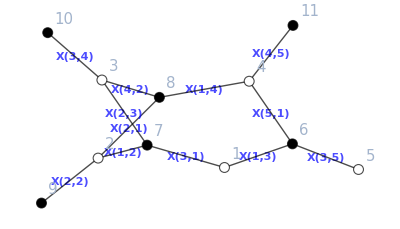

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=16;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```